## NN-Based Predictions of Intra-Season Performance Based on Junior Test Results (M)

List of athlete data from US national training camps. USSA points are an O.K metric of athlete performance, but do tend to sway towards sprinters :)

```mathematica
Take[a,20,19]//TableForm
```

First Name | Last Name | Year of Birth | Region | USSA Points | Sex | Qualified | Location | Estimated Elevation | 3,000 m Test Seconds | 1,000 meter DP Erg | Afton Coulee DP Test | Rollerski agility | Strength Test Sum | Pull Ups | Sit Ups | Push Ups | Box Jumps (16in) | Dips
Phoebe | Sweet | 2000 | East | 136.57 | Female | Y | Craftsbury VT |  | 702 | 0 | 0 | 0 | 199 | 10 | 50 | 40 | 52 | 27
Nina | Seemann | 2002 | East | 121.54 | Female | Y | Craftsbury VT |  | 795 | 243 | 0 | 0 | 258 | 15 | 65 | 53 | 54 | 41
Camille | Bolduc | 2003 | East | 201.92 | Female | Y | Craftsbury VT |  | 699 | 0 | 0 | 0 | 183 | 8 | 56 | 41 | 42 | 20
Lil Q | Massey-Bierman | 2003 | East | 198.71 | Female | Y | Craftsbury VT |  | 713 | 0 | 0 | 0 | 231 | 15 | 53 | 38 | 60 | 35
Maggie | McGee | 2004 | East | 231.52 | Female | Y | Craftsbury VT |  | 696 | 0 | 0 | 0 | 197 | 8 | 50 | 32 | 54 | 37
Adrienne | Remick | 2002 | East | 221.76 | Female | Y | Craftsbury VT |  | 725 | 0 | 0 | 0 | 228 | 13 | 53 | 43 | 60 | 33
Emma | Charles | 2004 | East | 231.6 | Female | Y | Oakland, ME |  | 783 | 255 | 0 | 0 | 175 | 6 | 48 | 35 | 44 | 30
Evie | Walton | 2004 | East | 189.82 | Female | Y | Keene Valley, NY |  | 809 | 0 | 0 | 0 | 188 | 6 | 51 | 35 | 57 | 27
Amelia | Tucker | 2002 | East | 176.99 | Female | Y | MA |  | 755 | 0 | 0 | 0 | 168 | 5 | 40 | 28 | 54 | 31
Sofia | Scirica | 2004 | East | 155.61 | Female | Y | MA |  | 728 | 0 | 0 | 0 | 213 | 12 | 52 | 47 | 58 | 20
Mica | Bodkins | 2004 | East | 214.32 | Female | Y | MA |  | 731 | 0 | 0 | 0 | 221 | 13 | 56 | 47 | 50 | 29
Shea | Brams | 2002 | East | 177.26 | Female | Y | Hanover NH |  | 715 | 0 | 0 | 0 | 196 | 8 | 46 | 36 | 57 | 33
Ava | Thurston | 2004 | East | 145.22 | Female | Y | Mansfield Nordic |  | 665 | 282 | 0 | 0 | 221 | 11 | 52 | 47 | 60 | 29
Rose | Clayton | 2001 | East | 205.69 | Female | Y | Mansfield Nordic |  | 706 | 0 | 0 | 0 | 122 | 0 | 43 | 20 | 46 | 13
Hattie | Barker | 2004 | East | 219.17 | Female | Y | Mansfield Nordic |  | 687 | 0 | 0 | 0 | 135 | 0 | 37 | 32 | 46 | 20
Samantha | Nolan | 2002 | East | 213.43 | Female | Y | Mansfield Nordic |  | 827 | 0 | 0 | 0 | 139 | 2 | 51 | 25 | 48 | 9
Finnegan | Mittelstadt | 2004 | East | 223.73 | Female | Y | Mansfield Nordic |  | 658 | 275 | 0 | 0 | 175 | 2 | 53 | 40 | 45 | 31
Callie | Young | 2000 | East | 117.3 | Female | Y |  |  | 731 | 0 | 0 | 0 | 245 | 15 | 59 | 43 | 64 | 34
Maddie | RelyeaÊ | 2002 | East | 246.05 | Female | Y | Mayfield NY |  | 709 | 0 | 0 | 0 |  |  |  |  |  |

Here is a set of men with their 3k time (sec), pull-ups, and push-ups -> USSA points. We can use the Predict[] function to create a linear-regression function, or small-NN to get an idea of what variables matter in athlete performance.

```mathematica
trainingset={{605,15,35}->159.78,{614,11,44}->164.63,{586,27,60}->110.23,{673,19,48}->160.61,{694,23,60}->256.83,{656,9,32}->241.39,{653,8,48}->149.08,{679,29,62}->185.41,{591,15,54}->98.12,{578,16,37}->233.01,{642,9,41}->126.76,{666,9,52}->195.43,{685,22,60}->154.05,{665,19,53}->169.14,{731,8,54}->355.01,{649,18,59}->159.86,{675,22,58}->251.46,{585,22,57}->146.86}
```

```mathematica
p=Predict[trainingset,Method->"NeuralNetwork"]
q=Predict[trainingset,Method->"LinearRegression"]
```

PredictorFunction[…]

PredictorFunction[…]

Interestingly enough, the linear regression for this small dataset suggests for men that pullup/pushup strength correlates strongly ~1 unit per pushup/pullup with USSA points. Since it is easier to do more pushups, pushups correlate probably the most with USSA points, then.  3k time, which might be on the order of ~40-50x less more than pull-ups, has a relatively smaller coefficient .08 in the linear regression, but when multiplied by 50x.08 =4, so the 3k time is a very strong predictor on men’s performance.

```mathematica
PredictorInformation[q,"Function"]
```

311.009-0.08698 #1-1.05604 #2-1.26581 #3&

```mathematica
trainingset=Table[Table[a[[j]][[i]],{i,{6,10,15,17}}]->a[[j]][[5]],{j,100,200}]
```

```mathematica
pm=PredictorMeasurements[p,{{601,16,53}->171.93,{664,24,61}->152.04,{624,11,34}->172.67,{573,21,62}->140.39,{597,23,49}->96.13,{585,8,54}->158.5,{573,21,62}->140.39,{597,23,49}->96.13,{585,8,54}->158.5,{611,12,49}->164.63,{620,19,69}->222.78,{624,11,34}->172.67,{737,24,47}->335.28}]
pm2=PredictorMeasurements[q,{{601,16,53}->171.93,{664,24,61}->152.04,{624,11,34}->172.67,{573,21,62}->140.39,{597,23,49}->96.13,{585,8,54}->158.5,{573,21,62}->140.39,{597,23,49}->96.13,{585,8,54}->158.5,{611,12,49}->164.63,{620,19,69}->222.78,{624,11,34}->172.67,{737,24,47}->335.28}]
```

```mathematica
{Information[p],Information[q]}
```

{Predictor information
Data type | {Numerical,Numerical,Numerical}
Standard deviation | 64.3 ± 14.
Method | NeuralNetwork
Single evaluation time | 2.24 ms/example
Batch evaluation speed | 53.7 examples/ms
Loss | 7.86 ± 1.8
Model memory | 240. kB
Training examples used | 18 examples
Training time | 2.36 s,Predictor information
Data type | {Numerical,Numerical,Numerical}
Standard deviation | 59.8 ± 10.
Method | LinearRegression
Single evaluation time | 1.54 ms/example
Batch evaluation speed | 337. examples/ms
Loss | 5.55 ± 0.19
Model memory | 205. kB
Training examples used | 18 examples
Training time | 727. ms}

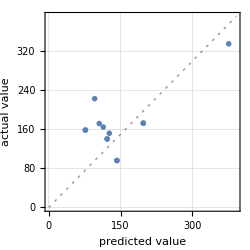
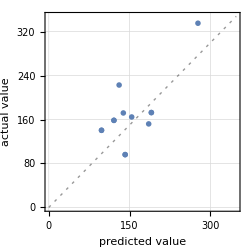
{Predictor Measurements
Predictor method | NeuralNetwork
Number of test examples | 13
Standard deviation | 58.8 ± 11.
Standard deviation baseline | 57.7 ± 20.
R-squared | -0.0383 ± 0.88
Mean cross entropy | 8.99 ± 1.8
Single evaluation time | 2.57 ms/example
Batch evaluation speed | 306. examples/s
-Graphics- | ,Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 13
Standard deviation | 44.3 ± 6.8
Standard deviation baseline | 57.7 ± 20.
R-squared | 0.411 ± 0.49
Mean cross entropy | 5.23 ± 0.11
Single evaluation time | 1.62 ms/example
Batch evaluation speed | 194. examples/s
-Graphics- | }

```mathematica
{pm,pm2}
```

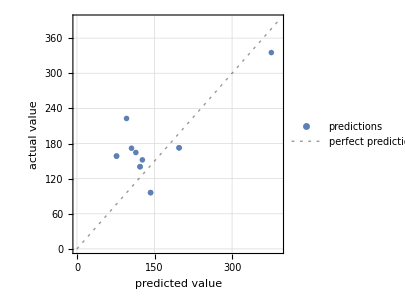
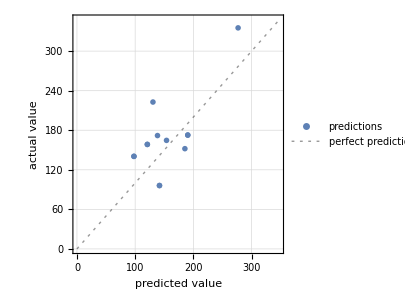

```mathematica
{pm["ComparisonPlot"],pm2["ComparisonPlot"]}
```

This is an online calculator that uses WL CloudDeploy to see these correlations.

```mathematica
CloudDeploy[Manipulate[{x,x1,x3}->p[{x,x1,x3}],{{x,0,Style["3k TT (sec)",24]},0,1000},{{x1,0,Style["Pullups #",24]},0,50},{{x3,0,Style["Pushups #",24]},0,50}]]
```

```mathematica
Take[a,8,8]//TableForm
```

First Name | Last Name | Year of Birth | Region | USSA Points | Sex | Qualified | Location
Phoebe | Sweet | 2000 | East | 136.57 | Female | Y | Craftsbury VT
Nina | Seemann | 2002 | East | 121.54 | Female | Y | Craftsbury VT
Camille | Bolduc | 2003 | East | 201.92 | Female | Y | Craftsbury VT
Lil Q | Massey-Bierman | 2003 | East | 198.71 | Female | Y | Craftsbury VT
Maggie | McGee | 2004 | East | 231.52 | Female | Y | Craftsbury VT
Adrienne | Remick | 2002 | East | 221.76 | Female | Y | Craftsbury VT
Emma | Charles | 2004 | East | 231.6 | Female | Y | Oakland, ME

```mathematica
trainingset={{605,15,35,67,45}->159.78,{614,11,44,57,45}->164.63,{586,27,60,63,45}->110.23,{673,19,48,49,34}->160.61,{694,23,60,59,34}->256.83,{656,9,32,66,30}->241.39,{653,8,48,57,46}->149.08,{679,29,62,61,42}->185.41,{591,15,54,69,26}->98.12,{578,16,37,63,34}->233.01,{642,9,41,76,20}->126.76,{666,9,52,75,28}->195.43,{685,22,60,66,56}->154.05,{665,19,53,78,36}->169.14,{731,8,54,66,54}->355.01,{649,18,59,61,40}->159.86,{675,22,58,67,22}->251.46}
```

```mathematica
p2=Predict[trainingset,Method->"NeuralNetwork"]
q2=Predict[trainingset,Method->"LinearRegression"]
```

PredictorFunction[…]

PredictorFunction[…]

```mathematica
p2m=PredictorMeasurements[p2,{{665,1,30,62,25}->219.17,{770,8,44,52,30}->231.6,{700,14,35,54,29}->214.42,{810,10,34,65,28}->229.23,{722,9,49,55,37}->181.47,{761,4,39,50,40}->187.52,{794,5,31,42,33}->232.97,{710,17,36,46,29}->184.39,{742,4,40,61,15}->199.15,{0,4,34,61,27}->164.26,{715,8,43,54,23}->157.23,{713,10,53,67,53}->153.67,{601,16,53,62,32}->171.93,{664,24,61,63,45}->152.04,{624,11,34,64,42}->172.67,{665,1,30,62,25}->219.17,{770,8,44,52,30}->231.6,{700,14,35,54,29}->214.42,{728,12,60,65,34}->155.61,{624,11,34,64,42}->172.67,{737,24,47,59,31}->335.28,{638,25,50,58,46}->275.08,{620,19,69,58,54}->222.78}]
q2m2=PredictorMeasurements[q2,{{665,1,30,62,25}->219.17,{770,8,44,52,30}->231.6,{700,14,35,54,29}->214.42,{810,10,34,65,28}->229.23,{722,9,49,55,37}->181.47,{761,4,39,50,40}->187.52,{794,5,31,42,33}->232.97,{710,17,36,46,29}->184.39,{742,4,40,61,15}->199.15,{0,4,34,61,27}->164.26,{715,8,43,54,23}->157.23,{713,10,53,67,53}->153.67,{601,16,53,62,32}->171.93,{664,24,61,63,45}->152.04,{624,11,34,64,42}->172.67,{665,1,30,62,25}->219.17,{770,8,44,52,30}->231.6,{700,14,35,54,29}->214.42,{728,12,60,65,34}->155.61,{624,11,34,64,42}->172.67,{737,24,47,59,31}->335.28,{638,25,50,58,46}->275.08,{620,19,69,58,54}->222.78}]
```

```mathematica
{Information[p2],Information[q2]}
```

{Predictor information
Data type | Mixed (number: 5)
Standard deviation | 64.4 ± 18.
Method | NeuralNetwork
Single evaluation time | 2.67 ms/example
Batch evaluation speed | 51. examples/ms
Loss | 8.21 ± 2.9
Model memory | 355. kB
Training examples used | 17 examples
Training time | 4.07 s,Predictor information
Data type | Mixed (number: 5)
Standard deviation | 56.7 ± 8.8
Method | LinearRegression
Single evaluation time | 1.62 ms/example
Batch evaluation speed | 357. examples/ms
Loss | 5.53 ± 0.067
Model memory | 219. kB
Training examples used | 17 examples
Training time | 842. ms}

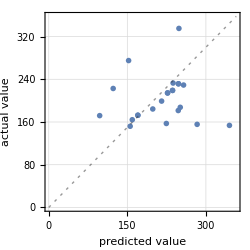
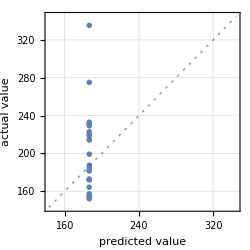
{Predictor Measurements
Predictor method | NeuralNetwork
Number of test examples | 23
Standard deviation | 68.1 ± 13.
Standard deviation baseline | 42.6 ± 9.
R-squared | -1.55 ± 1.5
Mean cross entropy | 12.7 ± 3.4
Single evaluation time | 2.88 ms/example
Batch evaluation speed | 549. examples/s
-Graphics- | ,Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 23
Standard deviation | 45.9 ± 11.
Standard deviation baseline | 42.6 ± 9.
R-squared | -0.156 ± 0.75
Mean cross entropy | 5.44 ± 0.082
Single evaluation time | 1.85 ms/example
Batch evaluation speed | 300. examples/s
-Graphics- | }

```mathematica
{p2m,q2m2}
```

```mathematica
{p2m,q2m2}
```

{Predictor Measurements
Predictor method | NeuralNetwork
Number of test examples | 23
Standard deviation | 68.1 ± 13.
Standard deviation baseline | 42.6 ± 9.
R-squared | -1.55 ± 1.5
Mean cross entropy | 12.7 ± 3.4
Single evaluation time | 2.88 ms/example
Batch evaluation speed | 549. examples/s
-Graphics- | ,Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 23
Standard deviation | 45.9 ± 11.
Standard deviation baseline | 42.6 ± 9.
R-squared | -0.156 ± 0.75
Mean cross entropy | 5.44 ± 0.082
Single evaluation time | 1.85 ms/example
Batch evaluation speed | 300. examples/s
-Graphics- | }

```mathematica
a={{"First Name","Last Name","Year of Birth","Region","USSA Points","Sex","Qualified","Location","Estimated Elevation","3,000 m Test Seconds","1,000 meter DP Erg","Afton Coulee DP Test","Rollerski agility","Strength Test Sum","Pull Ups","Sit Ups","Push Ups","Box Jumps (16in)","Dips","Strength Test Sum"},{"Phoebe","Sweet",2000,"East",136.57,"Female","Y","Craftsbury VT","",702,0,0,0,199,10,50,40,52,27,199},{"Nina","Seemann",2002,"East",121.54,"Female","Y","Craftsbury VT","",795,243,0,0,258,15,65,53,54,41,258},{"Camille","Bolduc",2003,"East",201.92,"Female","Y","Craftsbury VT","",699,0,0,0,183,8,56,41,42,20,183},{"Lil Q","Massey-Bierman",2003,"East",198.71,"Female","Y","Craftsbury VT","",713,0,0,0,231,15,53,38,60,35,231},{"Maggie","McGee",2004,"East",231.52,"Female","Y","Craftsbury VT","",696,0,0,0,197,8,50,32,54,37,197},{"Adrienne","Remick",2002,"East",221.76,"Female","Y","Craftsbury VT","",725,0,0,0,228,13,53,43,60,33,228},{"Emma","Charles",2004,"East",231.6,"Female","Y","Oakland, ME","",783,255,0,0,175,6,48,35,44,30,175},{"Evie","Walton",2004,"East",189.82,"Female","Y","Keene Valley, NY","",809,0,0,0,188,6,51,35,57,27,188},{"Amelia","Tucker",2002,"East",176.99,"Female","Y","MA","",755,0,0,0,168,5,40,28,54,31,168},{"Sofia","Scirica",2004,"East",155.61,"Female","Y","MA","",728,0,0,0,213,12,52,47,58,20,213},{"Mica","Bodkins",2004,"East",214.32,"Female","Y","MA","",731,0,0,0,221,13,56,47,50,29,221},{"Shea","Brams",2002,"East",177.26,"Female","Y","Hanover NH","",715,0,0,0,196,8,46,36,57,33,196},{"Ava","Thurston",2004,"East",145.22,"Female","Y","Mansfield Nordic","",665,282,0,0,221,11,52,47,60,29,221},{"Rose","Clayton",2001,"East",205.69,"Female","Y","Mansfield Nordic","",706,0,0,0,122,0,43,20,46,13,122},{"Hattie","Barker",2004,"East",219.17,"Female","Y","Mansfield Nordic","",687,0,0,0,135,0,37,32,46,20,135},{"Samantha","Nolan",2002,"East",213.43,"Female","Y","Mansfield Nordic","",827,0,0,0,139,2,51,25,48,9,139},{"Finnegan","Mittelstadt",2004,"East",223.73,"Female","Y","Mansfield Nordic","",658,275,0,0,175,2,53,40,45,31,175},{"Callie","Young",2000,"East",117.3,"Female","Y","","",731,0,0,0,245,15,59,43,64,34,245},{"Maddie","RelyeaÊ",2002,"East",246.05,"Female","Y","Mayfield NY","",709,0,0,0,"","","","","","",""},{"Grace","MatternÊ",2003,"East",229.22,"Female","Y","Brighton NYÊ","",710,260,0,0,163,3,48,37,51,18,163},{"Zofia","Stefankovic",2002,"East",236.07,"Female","Y","Brighton NYÊ","",736,260,0,0,175,13,38,36,36,26,175},{"Elsa","Bolinger",2003,"East",212.14,"Female","Y","Lyme, NH","",683,242,0,0,180,6,44,24,62,32,180},{"Emma","Strack",2002,"East",217.25,"Female","Y","GMVS","",766,256,0,0,"",4,51,34,33,41,""},{"Finnegan","Mittelstadt",2004,"East",223.73,"Female","Y","Hinesburg, VT","",658,275,0,0,175,2,53,40,45,31,175},{"Sam","Murray",2003,"East",159.78,"Male","Y","Hanover NH","",605,220,0,0,238,15,46,35,67,45,238},{"Jack","Lange",2004,"East",164.63,"Male","Y","Lyme NH","",614,235,0,0,229,11,50,44,57,45,229},{"Finn","Sweet",2002,"East",110.23,"Male","Y","Craftsbury VT","",586,211,0,0,305,27,56,60,63,45,305},{"Quinn","Wilson",2002,"East",160.61,"Male","Y","Dublin, NH","",673,226,0,0,228,19,40,48,49,34,228},{"Clint","Macy",2004,"East",256.83,"Male","Y","Dublin, NH","",694,240,0,0,274,23,52,60,59,34,274},{"Caden","Cote",2004,"East",241.39,"Male","Y","Oakland, ME","",656,229,0,0,202,9,47,32,66,30,202},{"Linden","Niedeck",2002,"East",149.08,"Male","Y","MAÊ","",653,216,0,0,214,8,39,48,57,46,214},{"Adam","Carlisle",2002,"East",185.41,"Male","Y","Amherst, MA","",679,0,0,0,325,29,73,62,61,42,325},{"Brian","Bushey",2002,"East",98.12,"Male","Y","GMVS","",591,213,0,0,241,15,47,54,69,26,241},{"Cormac","Leahy",2004,"East",233.01,"Male","Y","Craftsbury VT","",578,0,0,0,234,16,52,37,63,34,234},{"Aidan","Burt",2003,"East",126.76,"Male","Y","GMVS","",642,213,0,0,209,9,45,41,76,20,209},{"Fin","Bailey",2005,"East",195.43,"Male","Y","Peru VT","",666,218,0,0,237,9,55,52,75,28,237},{"Jack","Young",2002,"East",154.05,"Male","Y","Craftsbury VT","",685,0,0,0,298,22,50,60,66,56,298},{"Trey","Jones",2004,"East",169.14,"Male","Y","Steamboat Springs CO","",665,0,0,0,275,19,51,53,78,36,275},{"Jack","Christner",2002,"East",147.24,"Male","Y","Frost Mountain","",0,0,0,0,"","","","","","",""},{"Rena","Schwartz",1999,"East",125.77,"Female","N","Craftsbury VT","",637,268,0,0,231,14,53,50,61,25,231},{"Avery","Ellis",1998,"East",125.24,"Female","N","Craftsbury VT","",685,240,0,0,253,14,54,54,70,33,253},{"Emelia","JordanÊ",2005,"East",303.82,"Female","N","Brighton NYÊ","",776,298,0,0,143,2,39,31,40,27,143},{"Cathrine","Anzellotti",2005,"East","","Female","N","Brighton NYÊ","",679,284,0,0,154,0,50,33,42,29,154},{"Liza","Bell",2004,"East",310.96,"Female","N","Putney, VT","",0,258,0,0,199,3,44,39,58,49,199},{"Charlotte","Brown",2001,"East",222.1,"Female","N","St Paul, MN","",734,258,0,0,154,7,46,25,38,24,154},{"Amanda","Vansant",2002,"East",289.46,"Female","N","Holderness Nordic","",0,270,0,0,81,0,41,20,"",20,81},{"Lilly","Magnus",2002,"East",405.59,"Female","N","Holderness Nordic","",1060,285,0,0,85,2,30,25,"",24,85},{"Mae","Whitcomb",2003,"East",239.02,"Female","N","Holderness Nordic","",827,284,0,0,88,3,41,16,"",22,88},{"Reid","Donovan","","East","","Female","N","Holderness Nordic","",0,0,0,0,64,0,33,15,"",16,64},{"Kelsey","Maine","","East","","Female","N","Holderness Nordic","",0,0,0,0,78,1,44,20,"",11,78},{"Adah","Chapman","","East","","","N","Holderness Nordic","",0,0,0,0,99,4,43,25,"",19,99},{"Sam","Clark",2003,"East",314.61,"Male","N","Craftsbury VT","",0,0,0,0,214,14,42,50,50,30,214},{"Jed","Kurts",2003,"East",196.95,"Male","N","Craftsbury VT","",0,0,0,0,273,20,55,55,53,50,273},{"Chip","Freeman",2005,"East",355.01,"Male","N","Peru VT","",731,270,0,0,252,8,54,54,66,54,252},{"Jasper","Henderson",2002,"East","","Male","N","Craftsbury VT","",0,0,0,0,231,11,57,41,60,40,231},{"Gunnar","Caldwell",2004,"East","","Male","N","Putney, VT","",0,262,0,0,163,5,36,43,53,16,163},{"Omar","ArbrusterÊ",2003,"East","","Male","N","Honeoye Falls NY","",618,252,0,0,235,15,44,43,58,45,235},{"Jack","HulseyÊ",2003,"East","","Male","N","Honeoye Falls NY","",647,249,0,0,283,21,43,62,64,51,283},{"Liam","Judd",2003,"East","","Male","N","Brighton NYÊ","",725,252,0,0,195,6,42,45,50,40,195},{"Alex","Pogharien",2002,"East","","Male","N","Pittsford NYÊ","",707,243,0,0,202,10,41,41,45,45,202},{"Paul","Mason","","East","","Male","N","Holderness Nordic","",0,0,0,0,68,2,26,14,"",22,68},{"Charlie","Dobson","","East","","Male","N","Holderness Nordic","",693,0,0,0,245,30,59,46,"",50,245},{"Surya","Amundsen",2003,"East","","Male","N","Oakland, ME","",808,298,0,0,164,2,45,35,47,31,164},{"Keya","Amundsen",2004,"East","","Male","N","Oakland, ME","",928,311,0,0,109,3,35,20,30,15,109},{"Charles","Martell",2002,"East","","","N","Mansfield Nordic","",598,0,0,0,"","","","","","",""},{"Silas","Brown",2002,"East","","","N","Mansfield Nordic","",653,0,0,0,215,13,49,40,58,29,215},{"Niko","Cuneo",2007,"East","","","N","Mansfield Nordic","",665,0,0,0,"","","","","","",""},{"Taylor","Carlson",2006,"East","","","N","Mansfield Nordic","",721,0,0,0,136,3,30,39,34,24,136},{"Jax","Lubkowitz",2002,"East","","","N","Mansfield Nordic","",739,0,0,0,"","","","","","",""},{"Carl","Priganc",2006,"East","","","N","Mansfield Nordic","",777,0,0,0,177,5,57,45,30,30,177},{"Lily","Porth",2001,"East","","Female","N","Mansfield Nordic","",719,0,0,0,192,8,45,37,58,30,192},{"Julia","Thurston",2006,"East","","Female","N","Mansfield Nordic","",727,0,0,0,143,6,47,26,38,14,143},{"Isabelle","Serrano",2003,"East","","Female","N","Craftsbury/MNC","",754,0,0,0,"","","","","","",""},{"Julia","Oliver",2002,"East","","Female","N","Mansfield Nordic","",819,0,0,0,162,3,52,43,38,20,162},{"Ali","Priganc",2002,"East","","","N","Mansfield Nordic","",819,0,0,0,150,3,36,40,40,25,150},{"Hanna","Holm",2003,"East","","Female","N","Mansfield Nordic","",844,0,0,0,164,6,45,33,47,21,164},{"Virginia","Cobb",2005,"East","","Female","N","Mansfield Nordic","",870,0,0,0,120,0,44,31,30,15,120},{"Jessie","Kennedy",2003,"East","","Female","N","Mansfield Nordic","",941,0,0,0,"","","","","","",""},{"Evan","Grover",2004,"East","","Male","N","Bend Oregon","",635,250,0,0,181,14,37,53,55,27,181},{"Anja","Grover",2004,"East","","","N","Sun Valley Idaho","",1108,0,0,0,"",7,41,39,54,31,""},{"Fran","Peterson",2005,"Central",355.61,"Female","Y","BarronÊ",1150,713,288,0,0,175,4,45,32,39,47,175},{"Margo","Nightingale",2005,"Central",232.11,"Female","Y","Minneapolis MN",630,0,0,0,84,0,"","","","","",0},{"Morgan","Richter",2001,"Central",235.9,"Female","Y","Minneapolis MN",630,638,0,478,132,209,6,68,46,47,30,209},{"Jasper","Johnston",2003,"Central",159.86,"Male","Y","Ely",800,649,210,0,0,261,18,49,59,61,40,261},{"Owen","Williams",2004,"Central",251.46,"Male","Y","Stevens Point,WI",1090,675,194,0,0,268,22,55,58,67,22,268},{"Isak","Nightingale",2003,"Central",175.88,"Male","Y","Minneapolis MN",630,0,0,0,65,0,"","","","","",0},{"VictorÊ","Sparks",2003,"Central",183.1,"Male","Y","Minneapolis MN",630,616,0,407,66,297,22,70,50,60,51,297},{"Jon","Clarke",2004,"Central","","Male","Y","Minneapolis MN",630,652,0,435,67,234,23,60,32,48,25,234},{"Adrik","Kraftson",2004,"Central",241.48,"Male","Y","Minneapolis MN",630,578,0,392,72,277,20,66,55,59,37,277},{"Jon","Saldin",2004,"Central",286.77,"Male","Y","Minneapolis MN",630,671,0,458,0,0,"","","","","",0},{"Roger","Anderson",2003,"Central",146.86,"Male","Y","Minneapolis MN",630,585,0,0,0,319,22,52,57,62,82,319},{"Aidan","Earll","","Central","","","N","","",673,0,0,0,245,14,55,57,61,30,245},{"Bank","Bodor",2003,"Central","","","N","","",596,215,0,0,230,13,46,50,61,34,230},{"Casey","Van Hefty",2004,"Central","","","N","","",625,232,0,0,255,17,48,63,61,32,255},{"Grace","Kern","","Central","","","N","","",799,304,0,0,180,11,31,31,45,40,180},{"Caden","Albrecht",2003,"Central","","Male","N","Minneapolis MN",630,0,0,450,64,273,24,46,53,53,49,273},{"Jeff","Hodgson",2003,"Central","","Male","N","Minneapolis MN",630,0,0,525,78,169,3,68,25,47,20,169},{"Hariharam","Chidambaram",2003,"Central","","Male","N","Minneapolis MN",630,0,0,425,100,200,12,64,23,55,22,200},{"Magnus","O'Connor",2003,"Central","","Male","N","Minneapolis MN",630,0,0,444,75,218,10,55,36,63,34,218},{"Cooper","Camp",2003,"Central","","Male","N","Minneapolis MN",630,0,0,0,83,184,13,49,33,51,12,184},{"Nico","Alexander",2003,"Central","","Male","N","Minneapolis MN",630,0,0,418,95,202,13,62,33,58,10,202},{"Benon","Bettobro",2004,"Central","","Male","N","Minneapolis MN",630,0,0,426,85,"","","","","","",""},{"Leif","Sciroa",2003,"Central","","Male","N","Minneapolis MN",630,0,0,0,86,"","","","","","",""},{"Andrew","Defor",2004,"Central","","Male","N","Minneapolis MN",630,0,0,448,79,"","","","","","",""},{"Evan","O'Connor",2004,"Central","","Male","N","Minneapolis MN",630,0,0,462,77,167,3,54,28,56,20,167},{"Colin","Freed",2002,"Central","","Male","N","Minneapolis MN",630,0,0,444,75,381,32,68,80,69,68,381},{"Ericka","Peterson",2003,"Central","","Female","N","Minneapolis MN",630,0,0,737,86,148,1,67,18,41,19,148},{"Sophia","Pung",2004,"Central","","Female","N","Minneapolis MN",630,0,0,745,100,163,6,55,28,40,22,163},{"Johanna","Perry",2003,"Central","","Female","N","Minneapolis MN",630,0,0,692,126,135,0,57,30,30,18,135},{"Addie","Fabel",2004,"Central","","Female","N","Minneapolis MN",630,0,0,0,98,151,3,45,42,30,25,151},{"Eleanor","Wheeler",2003,"Central","","Female","N","Minneapolis MN",630,0,0,711,130,149,0,64,15,43,27,149},{"Laura","Pacala",2003,"Central","","Female","N","Minneapolis MN",630,0,0,755,120,153,1,58,27,48,17,153},{"Kathryn","House",2003,"Central","","Female","N","Minneapolis MN",630,0,0,640,113,168,0,68,17,48,35,168},{"Sierra","Larson",2004,"Central","","Female","N","Minneapolis MN",630,0,0,0,106,0,"","","","","",0},{"Etta","Luegers",2003,"Central","","Female","N","Minneapolis MN",630,0,0,557,98,103,2,50,28,"",19,103},{"Mila","Finch",2004,"Central","","Female","N","Minneapolis MN",630,0,0,560,115,192,2,57,39,58,32,192},{"EliÊ","Frenkel",2003,"Central","","Male","N","Minneapolis MN",630,0,0,466,0,200,13,55,39,43,24,200},{"Stas","Bednarski",2003,"Central","","Male","N","Minneapolis MN",630,0,0,460,0,0,"","","","","",0},{"Charlie","Grabow",2002,"Central","","Male","N","Minneapolis MN",630,0,0,440,0,255,23,51,41,60,34,255},{"Bergen","Thorson",2004,"Central","","Male","N","Minneapolis MN",630,0,0,488,0,0,"","","","","",0},{"Grete","Engels",2003,"Central","","Female","N","Minneapolis MN",630,0,0,0,0,167,7,56,24,42,24,167},{"Lexie","Madigan",2002,"West",229.23,"Female","Y","Truckee High School","",810,246,0,0,200,10,43,34,65,28,200},{"Annie","McColgan",2002,"West",181.47,"Female","Y","","",722,250,0,0,224,9,56,49,55,37,224},{"NovieÊ","McCabe",2001,"West",93.8,"Female","Y","Methow Valley WA","",660,255,0,0,0,"","","","","",0},{"Anja","Jensen",2002,"West",200.63,"Female","Y","Sun Valley","",757,258,0,0,0,"","","","","",0},{"Sidney","BarbierÊ",2003,"West",187.52,"Female","Y","Steamboat Springs","",761,270,0,0,192,4,51,39,50,40,192},{"Lily","Murnane",2003,"West",232.97,"Female","Y","Truckee High School","",794,289,0,0,164,5,43,31,42,33,164},{"Gretta","Scholz",2001,"West",184.39,"Female","Y","","",710,289,0,0,216,17,54,36,46,29,216},{"Kate","Oldham",2002,"West",142.1,"Female","Y","","",0,0,0,0,0,"","","","","",0},{"Molly","Blakslee",2002,"West",199.15,"Female","Y","","",742,0,0,0,172,4,44,40,61,15,172},{"Sarah","Bivens",2003,"West",164.26,"Female","Y","","",0,0,0,0,187,4,53,34,61,27,187},{"Haley","Brewster",2003,"West",157.23,"Female","Y","","",715,0,0,0,204,8,60,43,54,23,204},{"Emma","Reeder",2003,"West",153.67,"Female","Y","Vail, CO","",713,0,0,0,268,10,65,53,67,53,268},{"Walker","Hall",2002,"West",114.42,"Male","Y","","",0,210,0,0,0,"","","","","",0},{"Jack","Conde",2003,"West",171.93,"Male","Y","","",601,218,0,0,242,16,47,53,62,32,242},{"Lane","Myshrall",2001,"West",152.04,"Male","Y","park city","",664,223,0,0,299,24,58,61,63,45,299},{"Wes","Campbell",2004,"West",172.67,"Male","Y","","",624,226,0,0,227,11,54,34,64,42,227},{"Travis","Grialou",2002,"West",166.14,"Male","Y","","",0,227,0,0,170,22,40,48,"",16,170},{"Skylar","Patten",2001,"West",125.67,"Male","Y","Sun Valley","",589,232,0,0,0,"","","","","",0},{"Elijah","Weenig",2002,"West",124.89,"Male","Y","Sun Valley","",630,236,0,0,0,"","","","","",0},{"Logan","Moore",2002,"West",140.39,"Male","Y","Durango, Colorado","",573,236,0,0,273,21,40,62,50,58,273},{"Wally","Magill",2003,"West",96.13,"Male","Y","Steamboat Springs","",597,0,0,0,297,23,51,49,75,53,297},{"Carson","Williams",2002,"West",158.5,"Male","Y","Boulder, CO","",585,0,0,0,226,8,48,54,56,44,226},{"Nikolas","Burkhart",2001,"West",197.26,"Male","Y","","",0,0,0,0,"","","","","","",""},{"Seth","Wyatt",2001,"West",153.54,"Male","Y","","",0,0,0,0,"","","","","","",""},{"Cooper","Jones",2001,"West","","Male","Y","Steamboat Springs","",0,0,0,0,"","","","","","",""},{"HadassahÊ","Lurbur",2000,"West","","Female","N","Winthrop WA","",0,243,0,0,"","","","","","",""},{"GretaÊ","Laesch",2002,"West","","Female","N","winthrop WA","",708,0,0,0,"","","","","","",""},{"EvaÊ","Weymuller",2003,"West","","Female","N","winthrop WA","",812,0,0,0,163,9,44,25,46,21,163},{"Dashe","McCabe",2006,"West","","Female","N","winthrop WA","",772,0,0,0,210,20,39,42,49,20,210},{"Carter","Sheley",2005,"West","","Male","N","winthrop WA","",662,0,0,0,198,14,48,46,47,15,198},{"Graham","Sheley",2005,"West","","Male","N","winthrop WA","",641,0,0,0,229,19,41,60,47,24,229},{"Jori","Grialou",2004,"West","","Female","N","winthrop WA","",735,0,0,0,162,12,40,39,37,10,162},{"MariahÊ","Lucy",2004,"West","","Female","N","winthrop WA","",856,0,0,0,"","","","","","",""},{"Bordes","Etienne","","West","","Male","N","Truckee CA","",624,0,0,0,"","","","","","",""},{"Cuneo","Steffen","","West","","Male","N","Truckee CA","",628,0,0,0,"","","","","","",""},{"Deluna","Matthew","","West","","Male","N","Truckee CA","",737,0,0,0,"","","","","","",""},{"Lehmkuhl","Kili","","West","","Female","N","Truckee CA","",739,0,0,0,"","","","","","",""},{"Garso","Jackie","","West","","Female","N","Truckee CA","",762,0,0,0,"","","","","","",""},{"Feland","Zandra","","West","","Female","N","Truckee CA","",794,0,0,0,"","","","","","",""},{"Powell","Alani","","West","","Female","N","Truckee CA","",799,0,0,0,"","","","","","",""},{"Scott","Keira","","West","","Female","N","Truckee CA","",801,0,0,0,"","","","","","",""},{"Hammond","Hannah","","West","","Female","N","Truckee CA","",830,0,0,0,"","","","","","",""},{"Cutler","Ben","","West","","Male","N","Truckee CA","",860,0,0,0,"","","","","","",""},{"Schoonmaker","Mera","","West","","Female","N","Truckee CA","",871,0,0,0,"","","","","","",""},{"Jake","SteevesÊ","","West","","Male","N","Boulder, CO","",0,0,0,0,210,9,42,35,68,38,210},{"Sam","BrooksÊ","","West","","Male","N","Boulder, CO","",0,0,0,0,290,19,60,63,51,59,290},{"Samuel","Berets","","West","","Male","N","Boulder, CO","",0,0,0,0,276,13,61,52,52,72,276},{"Samuel","Gurarie","","West","","Male","N","Boulder, CO","",0,0,0,0,130,7,34,28,32,15,130},{"Lucas","Martens","","West","","Male","N","Boulder, CO","",0,0,0,0,263,16,48,62,57,48,263},{"Sophie","Spalding","","West","","Female","N","Boulder, CO","",0,0,0,0,242,10,50,61,50,51,242},{"Wettermark","Pascal",2006,"West","","Male","N","Truckee CA","",702,0,0,0,"","","","","","",""},{"Nygard","CJ",2005,"West","","Male","N","Truckee CA","",711,0,0,0,"","","","","","",""},{"Cisler","Grace","","West","","Female","N","Yuba City, CA","",799,0,0,0,"","","","","","",""},{"Hattie","Barker",2004,"National U16 Camp",219.17,"Female","Y","","",665,246,0,0,162,1,42,30,62,25,162},{"Emma","Charles",2004,"National U16 Camp",231.6,"Female","Y","","",770,250,0,0,200,8,50,44,52,30,200},{"Elena","Grissom",2004,"National U16 Camp",214.42,"Female","Y","","",700,255,0,0,202,14,42,35,54,29,202},{"Anja","Grover",2004,"National U16 Camp",235,"Female","Y","","",0,258,0,0,0,"","","","","",0},{"Hayden","McJunkin",2004,"National U16 Camp",253.17,"Female","Y","","",0,270,0,0,0,"","","","","",0},{"NatalieÊ","OÕBrien",2004,"National U16 Camp","","Female","Y","","",0,289,0,0,0,"","","","","",0},{"Elsa","Perkins",2004,"National U16 Camp",174.62,"Female","Y","","",0,289,0,0,205,9,64,35,59,20,205},{"Fran","Peterson",2005,"National U16 Camp",355.61,"Female","Y","","",674,0,0,0,196,7,46,39,44,46,196},{"Kaylynn","Sandall",2004,"National U16 Camp",298.09,"Female","Y","","",737,0,0,0,147,2,41,20,56,24,147},{"Nina","Schamberger",2005,"National U16 Camp",163.5,"Female","Y","","",684,0,0,0,258,13,64,55,69,31,258},{"Sofia","Scirica",2004,"National U16 Camp",155.61,"Female","Y","","",728,0,0,0,251,12,56,60,65,34,251},{"Ava","ThurstonÊ",2004,"National U16 Camp","","Female","Y","","",0,210,0,0,0,"","","","","",0},{"Fin","Bailey",2005,"National U16 Camp",195.43,"Male","Y","","",0,218,0,0,0,"","","","","",0},{"Wes","Campbell",2004,"National U16 Camp",172.67,"Male","Y","","",624,223,0,0,227,11,54,34,64,42,227},{"Matthew","DeLuna",2004,"National U16 Camp",335.28,"Male","Y","","",737,226,0,0,250,24,41,47,59,31,250},{"Ethan","Eski",2004,"National U16 Camp",275.08,"Male","Y","","",638,227,0,0,282,25,53,50,58,46,282},{"Phineas","Fischer",2004,"National U16 Camp",214.38,"Male","Y","","",0,232,0,0,0,"","","","","",0},{"Gavin","Galyardt",2005,"National U16 Camp",271.85,"Male","Y","","",0,236,0,0,181,8,26,45,51,35,181},{"Trey","Jones",2004,"National U16 Camp",169.14,"Male","Y","","",0,236,0,0,0,"","","","","",0},{"Max","Kluck",2004,"National U16 Camp",218.35,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Jack","Lange",2004,"National U16 Camp",164.63,"Male","Y","","",611,0,0,0,239,12,49,49,57,48,239},{"Clint","Macy",2004,"National U16 Camp",256.83,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Ben","Oldham",2005,"National U16 Camp",237.65,"Male","Y","","",0,0,0,0,220,19,42,32,60,29,220},{"Aaron","Power",2004,"National U16 Camp",222.78,"Male","Y","","",620,0,0,0,287,19,49,69,58,54,287},{"Derek","Richardson",2004,"National U16 Camp",241.4,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Griff","Rillos",2004,"National U16 Camp",211.74,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Matt","Seline",2004,"National U16 Camp",240.1,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Cole","Shockey",2004,"National U16 Camp",259.19,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Emmet","Shuman",2004,"National U16 Camp",437.75,"Male","Y","","",0,0,0,0,176,9,32,29,58,30,176},{"Noah","Straka",2004,"National U16 Camp",249.91,"Male","Y","","",617,0,0,0,306,32,50,60,50,50,306},{"MasonÊ","Wheeler",2004,"National U16 Camp",215.39,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Owen","Williams",2004,"National U16 Camp",251.46,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Tyler","Wright",2004,"National U16 Camp",225.91,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Kate","Oldham",2002,"National REG Only",142.1,"Female","Y","Truckee High School",5957,810,0,0,0,200,10,43,"",65,28,200},{"Lily","Murnane",2003,"National REG Only",232.97,"Female","Y","","",722,0,0,0,224,9,56,"",55,37,224},{"Nikolas","Burkhart",2001,"National REG Only",197.26,"Male","Y","Methow Valley WA",2000,660,0,0,0,0,"","","","","",0},{"Lexie","Madigan",2002,"National REG Only",229.23,"Female","Y","Sun Valley",5300,757,0,0,0,0,"","","","","",0},{"Carson","Williams",2002,"National REG Only",158.5,"Male","Y","Steamboat Springs",6750,761,0,0,0,192,4,51,"",50,40,192},{"Seth","Wyatt",2001,"National REG Only",153.54,"Male","Y","Truckee High School",5957,794,0,0,0,164,5,43,"",42,33,164},{"Logan","Moore",2002,"National REG Only",140.39,"Male","Y","",2000,710,0,0,0,216,17,54,"",46,29,216},{"Jack","Conde",2003,"National REG Only",171.93,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"NovieÊ","McCabe",2001,"National REG Only",93.8,"Female","Y","","",742,0,0,0,172,4,44,"",61,15,172},{"Gretta","Scholz",2001,"National REG Only",184.39,"Female","Y","","",0,0,0,0,187,4,53,"",61,27,187},{"Annie","McColgan",2002,"National REG Only",181.47,"Female","Y","","",715,0,0,0,204,8,60,"",54,23,204},{"Travis","Grialou",2002,"National REG Only",166.14,"Male","Y","Vail, CO",7400,713,0,0,0,268,10,65,"",67,53,268},{"Walker","Hall",2002,"National REG Only",114.42,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Lane","Myshrall",2001,"National REG Only",152.04,"Male","Y","","",601,0,0,0,242,16,47,"",62,32,242},{"Wes","Campbell",2004,"National REG Only",172.67,"Male","Y","park city",6755,664,0,0,0,299,24,58,"",63,45,299},{"Emma","Reeder",2003,"National REG Only",153.67,"Female","Y","",6755,624,0,0,0,227,11,54,"",64,42,227},{"Haley","Brewster",2003,"National REG Only",157.23,"Female","Y","","",0,0,0,0,170,22,40,"","",16,170},{"Molly","Blakslee",2002,"National REG Only",199.15,"Female","Y","Sun Valley",5300,589,0,0,0,0,"","","","","",0},{"Sarah","Bivens",2003,"National REG Only",164.26,"Female","Y","Sun Valley",5300,630,0,0,0,0,"","","","","",0},{"Sidney","BarbierÊ",2003,"National REG Only",187.52,"Female","Y","Durango, Colorado",6512,573,0,0,0,273,21,40,"",50,58,273},{"Cooper","Jones",2001,"National REG Only","","Male","Y","Steamboat Springs",6900,597,0,0,0,297,23,51,"",75,53,297},{"Wally","Magill",2003,"National REG Only",96.13,"Male","Y","Boulder, CO",5300,585,0,0,0,226,8,48,"",56,44,226},{"Anja","Jensen",2002,"National REG Only",200.63,"Female","Y","Sun Valley",5300,757,0,0,0,0,"","","","","",0},{"Elijah","Weenig",2002,"National REG Only",124.89,"Male","Y","",5300,0,0,0,0,0,"","","","","",0},{"Skylar","Patten",2001,"National REG Only",125.67,"Male","Y","Steamboat Springs",5300,0,0,0,0,0,"","","","","",0},{"Phoebe","Sweet",2000,"All",136.57,"Female","Y","Craftsbury VT","",702,0,0,0,199,10,50,40,52,27,199},{"Nina","Seemann",2002,"All",121.54,"Female","Y","Craftsbury VT","",795,243,0,0,258,15,65,53,54,41,258},{"Camille","Bolduc",2003,"All",201.92,"Female","Y","Craftsbury VT","",699,0,0,0,183,8,56,41,42,20,183},{"Lil Q","Massey-Bierman",2003,"All",198.71,"Female","Y","Craftsbury VT","",713,0,0,0,231,15,53,38,60,35,231},{"Maggie","McGee",2004,"All",231.52,"Female","Y","Craftsbury VT","",696,0,0,0,197,8,50,32,54,37,197},{"Adrienne","Remick",2002,"All",221.76,"Female","Y","Craftsbury VT","",725,0,0,0,228,13,53,43,60,33,228},{"Emma","Charles",2004,"All",231.6,"Female","Y","Oakland, ME","",783,255,0,0,175,6,48,35,44,30,175},{"Evie","Walton",2004,"All",189.82,"Female","Y","Keene Valley, NY","",809,0,0,0,188,6,51,35,57,27,188},{"Amelia","Tucker",2002,"All",176.99,"Female","Y","MA","",755,0,0,0,168,5,40,28,54,31,168},{"Sofia","Scirica",2004,"All",155.61,"Female","Y","MA","",728,0,0,0,213,12,52,47,58,20,213},{"Mica","Bodkins",2004,"All",214.32,"Female","Y","MA","",731,0,0,0,221,13,56,47,50,29,221},{"Shea","Brams",2002,"All",177.26,"Female","Y","Hanover NH","",715,0,0,0,196,8,46,36,57,33,196},{"Ava","Thurston",2004,"All",145.22,"Female","Y","Mansfield Nordic","",665,282,0,0,221,11,52,47,60,29,221},{"Rose","Clayton",2001,"All",205.69,"Female","Y","Mansfield Nordic","",706,0,0,0,122,0,43,20,46,13,122},{"Hattie","Barker",2004,"All",219.17,"Female","Y","Mansfield Nordic","",687,0,0,0,135,0,37,32,46,20,135},{"Samantha","Nolan",2002,"All",213.43,"Female","Y","Mansfield Nordic","",827,0,0,0,139,2,51,25,48,9,139},{"Finnegan","Mittelstadt",2004,"All",223.73,"Female","Y","Mansfield Nordic","",658,275,0,0,175,2,53,40,45,31,175},{"Callie","Young",2000,"All",117.3,"Female","Y","","",731,0,0,0,245,15,59,43,64,34,245},{"Maddie","RelyeaÊ",2002,"All",246.05,"Female","Y","Mayfield NY","",709,0,0,0,"","","","","","",""},{"Grace","MatternÊ",2003,"All",229.22,"Female","Y","Brighton NYÊ","",710,260,0,0,163,3,48,37,51,18,163},{"Zofia","Stefankovic",2002,"All",236.07,"Female","Y","Brighton NYÊ","",736,260,0,0,175,13,38,36,36,26,175},{"Elsa","Bolinger",2003,"All",212.14,"Female","Y","Lyme, NH","",683,242,0,0,180,6,44,24,62,32,180},{"Emma","Strack",2002,"All",217.25,"Female","Y","GMVS","",766,256,0,0,"",4,51,34,33,41,""},{"Finnegan","Mittelstadt",2004,"All",223.73,"Female","Y","Hinesburg, VT","",658,275,0,0,175,2,53,40,45,31,175},{"Sam","Murray",2003,"All",159.78,"Male","Y","Hanover NH","",605,220,0,0,238,15,46,35,67,45,238},{"Jack","Lange",2004,"All",164.63,"Male","Y","Lyme NH","",614,235,0,0,229,11,50,44,57,45,229},{"Finn","Sweet",2002,"All",110.23,"Male","Y","Craftsbury VT","",586,211,0,0,305,27,56,60,63,45,305},{"Quinn","Wilson",2002,"All",160.61,"Male","Y","Dublin, NH","",673,226,0,0,228,19,40,48,49,34,228},{"Clint","Macy",2004,"All",256.83,"Male","Y","Dublin, NH","",694,240,0,0,274,23,52,60,59,34,274},{"Caden","Cote",2004,"All",241.39,"Male","Y","Oakland, ME","",656,229,0,0,202,9,47,32,66,30,202},{"Linden","Niedeck",2002,"All",149.08,"Male","Y","MAÊ","",653,216,0,0,214,8,39,48,57,46,214},{"Adam","Carlisle",2002,"All",185.41,"Male","Y","Amherst, MA","",679,0,0,0,325,29,73,62,61,42,325},{"Brian","Bushey",2002,"All",98.12,"Male","Y","GMVS","",591,213,0,0,241,15,47,54,69,26,241},{"Cormac","Leahy",2004,"All",233.01,"Male","Y","Craftsbury VT","",578,0,0,0,234,16,52,37,63,34,234},{"Aidan","Burt",2003,"All",126.76,"Male","Y","GMVS","",642,213,0,0,209,9,45,41,76,20,209},{"Fin","Bailey",2005,"All",195.43,"Male","Y","Peru VT","",666,218,0,0,237,9,55,52,75,28,237},{"Jack","Young",2002,"All",154.05,"Male","Y","Craftsbury VT","",685,0,0,0,298,22,50,60,66,56,298},{"Trey","Jones",2004,"All",169.14,"Male","Y","Steamboat Springs CO","",665,0,0,0,275,19,51,53,78,36,275},{"Jack","Christner",2002,"All",147.24,"Male","Y","Frost Mountain","",0,0,0,0,"","","","","","",""},{"Rena","Schwartz",1999,"All",125.77,"Female","N","Craftsbury VT","",637,268,0,0,231,14,53,50,61,25,231},{"Avery","Ellis",1998,"All",125.24,"Female","N","Craftsbury VT","",685,240,0,0,253,14,54,54,70,33,253},{"Emelia","JordanÊ",2005,"All",303.82,"Female","N","Brighton NYÊ","",776,298,0,0,143,2,39,31,40,27,143},{"Cathrine","Anzellotti",2005,"All","","Female","N","Brighton NYÊ","",679,284,0,0,154,0,50,33,42,29,154},{"Liza","Bell",2004,"All",310.96,"Female","N","Putney, VT","",0,258,0,0,199,3,44,39,58,49,199},{"Charlotte","Brown",2001,"All",222.1,"Female","N","St Paul, MN","",734,258,0,0,154,7,46,25,38,24,154},{"Amanda","Vansant",2002,"All",289.46,"Female","N","Holderness Nordic","",0,270,0,0,81,0,41,20,"",20,81},{"Lilly","Magnus",2002,"All",405.59,"Female","N","Holderness Nordic","",1060,285,0,0,85,2,30,25,"",24,85},{"Mae","Whitcomb",2003,"All",239.02,"Female","N","Holderness Nordic","",827,284,0,0,88,3,41,16,"",22,88},{"Reid","Donovan","","All","","Female","N","Holderness Nordic","",0,0,0,0,64,0,33,15,"",16,64},{"Kelsey","Maine","","All","","Female","N","Holderness Nordic","",0,0,0,0,78,1,44,20,"",11,78},{"Adah","Chapman","","All","","","N","Holderness Nordic","",0,0,0,0,99,4,43,25,"",19,99},{"Sam","Clark",2003,"All",314.61,"Male","N","Craftsbury VT","",0,0,0,0,214,14,42,50,50,30,214},{"Jed","Kurts",2003,"All",196.95,"Male","N","Craftsbury VT","",0,0,0,0,273,20,55,55,53,50,273},{"Chip","Freeman",2005,"All",355.01,"Male","N","Peru VT","",731,270,0,0,252,8,54,54,66,54,252},{"Jasper","Henderson",2002,"All","","Male","N","Craftsbury VT","",0,0,0,0,231,11,57,41,60,40,231},{"Gunnar","Caldwell",2004,"All","","Male","N","Putney, VT","",0,262,0,0,163,5,36,43,53,16,163},{"Omar","ArbrusterÊ",2003,"All","","Male","N","Honeoye Falls NY","",618,252,0,0,235,15,44,43,58,45,235},{"Jack","HulseyÊ",2003,"All","","Male","N","Honeoye Falls NY","",647,249,0,0,283,21,43,62,64,51,283},{"Liam","Judd",2003,"All","","Male","N","Brighton NYÊ","",725,252,0,0,195,6,42,45,50,40,195},{"Alex","Pogharien",2002,"All","","Male","N","Pittsford NYÊ","",707,243,0,0,202,10,41,41,45,45,202},{"Paul","Mason","","All","","Male","N","Holderness Nordic","",0,0,0,0,68,2,26,14,"",22,68},{"Charlie","Dobson","","All","","Male","N","Holderness Nordic","",693,0,0,0,245,30,59,46,"",50,245},{"Surya","Amundsen",2003,"All","","Male","N","Oakland, ME","",808,298,0,0,164,2,45,35,47,31,164},{"Keya","Amundsen",2004,"All","","Male","N","Oakland, ME","",928,311,0,0,109,3,35,20,30,15,109},{"Charles","Martell",2002,"All","","","N","Mansfield Nordic","",598,0,0,0,"","","","","","",""},{"Silas","Brown",2002,"All","","","N","Mansfield Nordic","",653,0,0,0,215,13,49,40,58,29,215},{"Niko","Cuneo",2007,"All","","","N","Mansfield Nordic","",665,0,0,0,"","","","","","",""},{"Taylor","Carlson",2006,"All","","","N","Mansfield Nordic","",721,0,0,0,136,3,30,39,34,24,136},{"Jax","Lubkowitz",2002,"All","","","N","Mansfield Nordic","",739,0,0,0,"","","","","","",""},{"Carl","Priganc",2006,"All","","","N","Mansfield Nordic","",777,0,0,0,177,5,57,45,30,30,177},{"Lily","Porth",2001,"All","","Female","N","Mansfield Nordic","",719,0,0,0,192,8,45,37,58,30,192},{"Julia","Thurston",2006,"All","","Female","N","Mansfield Nordic","",727,0,0,0,143,6,47,26,38,14,143},{"Isabelle","Serrano",2003,"All","","Female","N","Craftsbury/MNC","",754,0,0,0,"","","","","","",""},{"Julia","Oliver",2002,"All","","Female","N","Mansfield Nordic","",819,0,0,0,162,3,52,43,38,20,162},{"Ali","Priganc",2002,"All","","","N","Mansfield Nordic","",819,0,0,0,150,3,36,40,40,25,150},{"Hanna","Holm",2003,"All","","Female","N","Mansfield Nordic","",844,0,0,0,164,6,45,33,47,21,164},{"Virginia","Cobb",2005,"All","","Female","N","Mansfield Nordic","",870,0,0,0,120,0,44,31,30,15,120},{"Jessie","Kennedy",2003,"All","","Female","N","Mansfield Nordic","",941,0,0,0,"","","","","","",""},{"Evan","Grover",2004,"All","","Male","N","Bend Oregon","",635,250,0,0,181,14,37,53,55,27,181},{"Anja","Grover",2004,"All","","","N","Sun Valley Idaho","",1108,0,0,0,"",7,41,39,54,31,""},{"Fran","Peterson",2005,"All",355.61,"Female","Y","BarronÊ",1150,713,288,0,0,175,4,45,32,39,47,175},{"Margo","Nightingale",2005,"All",232.11,"Female","Y","Minneapolis MN",630,0,0,0,84,0,"","","","","",0},{"Morgan","Richter",2001,"All",235.9,"Female","Y","Minneapolis MN",630,638,0,478,132,209,6,68,46,47,30,209},{"Jasper","Johnston",2003,"All",159.86,"Male","Y","Ely",800,649,210,0,0,261,18,49,59,61,40,261},{"Owen","Williams",2004,"All",251.46,"Male","Y","Stevens Point,WI",1090,675,194,0,0,268,22,55,58,67,22,268},{"Isak","Nightingale",2003,"All",175.88,"Male","Y","Minneapolis MN",630,0,0,0,65,0,"","","","","",0},{"VictorÊ","Sparks",2003,"All",183.1,"Male","Y","Minneapolis MN",630,616,0,407,66,297,22,70,50,60,51,297},{"Jon","Clarke",2004,"All","","Male","Y","Minneapolis MN",630,652,0,435,67,234,23,60,32,48,25,234},{"Adrik","Kraftson",2004,"All",241.48,"Male","Y","Minneapolis MN",630,578,0,392,72,277,20,66,55,59,37,277},{"Jon","Saldin",2004,"All",286.77,"Male","Y","Minneapolis MN",630,671,0,458,0,0,"","","","","",0},{"Roger","Anderson",2003,"All",146.86,"Male","Y","Minneapolis MN",630,585,0,0,0,319,22,52,57,62,82,319},{"Aidan","Earll","","All","","","N","","",673,0,0,0,245,14,55,57,61,30,245},{"Bank","Bodor",2003,"All","","","N","","",596,215,0,0,230,13,46,50,61,34,230},{"Casey","Van Hefty",2004,"All","","","N","","",625,232,0,0,255,17,48,63,61,32,255},{"Grace","Kern","","All","","","N","","",799,304,0,0,180,11,31,31,45,40,180},{"Caden","Albrecht",2003,"All","","Male","N","Minneapolis MN",630,0,0,450,64,273,24,46,53,53,49,273},{"Jeff","Hodgson",2003,"All","","Male","N","Minneapolis MN",630,0,0,525,78,169,3,68,25,47,20,169},{"Hariharam","Chidambaram",2003,"All","","Male","N","Minneapolis MN",630,0,0,425,100,200,12,64,23,55,22,200},{"Magnus","O'Connor",2003,"All","","Male","N","Minneapolis MN",630,0,0,444,75,218,10,55,36,63,34,218},{"Cooper","Camp",2003,"All","","Male","N","Minneapolis MN",630,0,0,0,83,184,13,49,33,51,12,184},{"Nico","Alexander",2003,"All","","Male","N","Minneapolis MN",630,0,0,418,95,202,13,62,33,58,10,202},{"Benon","Bettobro",2004,"All","","Male","N","Minneapolis MN",630,0,0,426,85,"","","","","","",""},{"Leif","Sciroa",2003,"All","","Male","N","Minneapolis MN",630,0,0,0,86,"","","","","","",""},{"Andrew","Defor",2004,"All","","Male","N","Minneapolis MN",630,0,0,448,79,"","","","","","",""},{"Evan","O'Connor",2004,"All","","Male","N","Minneapolis MN",630,0,0,462,77,167,3,54,28,56,20,167},{"Colin","Freed",2002,"All","","Male","N","Minneapolis MN",630,0,0,444,75,381,32,68,80,69,68,381},{"Ericka","Peterson",2003,"All","","Female","N","Minneapolis MN",630,0,0,737,86,148,1,67,18,41,19,148},{"Sophia","Pung",2004,"All","","Female","N","Minneapolis MN",630,0,0,745,100,163,6,55,28,40,22,163},{"Johanna","Perry",2003,"All","","Female","N","Minneapolis MN",630,0,0,692,126,135,0,57,30,30,18,135},{"Addie","Fabel",2004,"All","","Female","N","Minneapolis MN",630,0,0,0,98,151,3,45,42,30,25,151},{"Eleanor","Wheeler",2003,"All","","Female","N","Minneapolis MN",630,0,0,711,130,149,0,64,15,43,27,149},{"Laura","Pacala",2003,"All","","Female","N","Minneapolis MN",630,0,0,755,120,153,1,58,27,48,17,153},{"Kathryn","House",2003,"All","","Female","N","Minneapolis MN",630,0,0,640,113,168,0,68,17,48,35,168},{"Sierra","Larson",2004,"All","","Female","N","Minneapolis MN",630,0,0,0,106,0,"","","","","",0},{"Etta","Luegers",2003,"All","","Female","N","Minneapolis MN",630,0,0,557,98,103,2,50,28,"",19,103},{"Mila","Finch",2004,"All","","Female","N","Minneapolis MN",630,0,0,560,115,192,2,57,39,58,32,192},{"EliÊ","Frenkel",2003,"All","","Male","N","Minneapolis MN",630,0,0,466,0,200,13,55,39,43,24,200},{"Stas","Bednarski",2003,"All","","Male","N","Minneapolis MN",630,0,0,460,0,0,"","","","","",0},{"Charlie","Grabow",2002,"All","","Male","N","Minneapolis MN",630,0,0,440,0,255,23,51,41,60,34,255},{"Bergen","Thorson",2004,"All","","Male","N","Minneapolis MN",630,0,0,488,0,0,"","","","","",0},{"Grete","Engels",2003,"All","","Female","N","Minneapolis MN",630,0,0,0,0,167,7,56,24,42,24,167},{"Lexie","Madigan",2002,"All",229.23,"Female","Y","Truckee High School","",810,246,0,0,200,10,43,34,65,28,200},{"Annie","McColgan",2002,"All",181.47,"Female","Y","","",722,250,0,0,224,9,56,49,55,37,224},{"NovieÊ","McCabe",2001,"All",93.8,"Female","Y","Methow Valley WA","",660,255,0,0,0,"","","","","",0},{"Anja","Jensen",2002,"All",200.63,"Female","Y","Sun Valley","",757,258,0,0,0,"","","","","",0},{"Sidney","BarbierÊ",2003,"All",187.52,"Female","Y","Steamboat Springs","",761,270,0,0,192,4,51,39,50,40,192},{"Lily","Murnane",2003,"All",232.97,"Female","Y","Truckee High School","",794,289,0,0,164,5,43,31,42,33,164},{"Gretta","Scholz",2001,"All",184.39,"Female","Y","","",710,289,0,0,216,17,54,36,46,29,216},{"Kate","Oldham",2002,"All",142.1,"Female","Y","","",0,0,0,0,0,"","","","","",0},{"Molly","Blakslee",2002,"All",199.15,"Female","Y","","",742,0,0,0,172,4,44,40,61,15,172},{"Sarah","Bivens",2003,"All",164.26,"Female","Y","","",0,0,0,0,187,4,53,34,61,27,187},{"Haley","Brewster",2003,"All",157.23,"Female","Y","","",715,0,0,0,204,8,60,43,54,23,204},{"Emma","Reeder",2003,"All",153.67,"Female","Y","Vail, CO","",713,0,0,0,268,10,65,53,67,53,268},{"Walker","Hall",2002,"All",114.42,"Male","Y","","",0,210,0,0,0,"","","","","",0},{"Jack","Conde",2003,"All",171.93,"Male","Y","","",601,218,0,0,242,16,47,53,62,32,242},{"Lane","Myshrall",2001,"All",152.04,"Male","Y","park city","",664,223,0,0,299,24,58,61,63,45,299},{"Wes","Campbell",2004,"All",172.67,"Male","Y","","",624,226,0,0,227,11,54,34,64,42,227},{"Travis","Grialou",2002,"All",166.14,"Male","Y","","",0,227,0,0,170,22,40,48,"",16,170},{"Skylar","Patten",2001,"All",125.67,"Male","Y","Sun Valley","",589,232,0,0,0,"","","","","",0},{"Elijah","Weenig",2002,"All",124.89,"Male","Y","Sun Valley","",630,236,0,0,0,"","","","","",0},{"Logan","Moore",2002,"All",140.39,"Male","Y","Durango, Colorado","",573,236,0,0,273,21,40,62,50,58,273},{"Wally","Magill",2003,"All",96.13,"Male","Y","Steamboat Springs","",597,0,0,0,297,23,51,49,75,53,297},{"Carson","Williams",2002,"All",158.5,"Male","Y","Boulder, CO","",585,0,0,0,226,8,48,54,56,44,226},{"Nikolas","Burkhart",2001,"All",197.26,"Male","Y","","",0,0,0,0,"","","","","","",""},{"Seth","Wyatt",2001,"All",153.54,"Male","Y","","",0,0,0,0,"","","","","","",""},{"Cooper","Jones",2001,"All","","Male","Y","Steamboat Springs","",0,0,0,0,"","","","","","",""},{"HadassahÊ","Lurbur",2000,"All","","Female","N","Winthrop WA","",0,243,0,0,"","","","","","",""},{"GretaÊ","Laesch",2002,"All","","Female","N","winthrop WA","",708,0,0,0,"","","","","","",""},{"EvaÊ","Weymuller",2003,"All","","Female","N","winthrop WA","",812,0,0,0,163,9,44,25,46,21,163},{"Dashe","McCabe",2006,"All","","Female","N","winthrop WA","",772,0,0,0,210,20,39,42,49,20,210},{"Carter","Sheley",2005,"All","","Male","N","winthrop WA","",662,0,0,0,198,14,48,46,47,15,198},{"Graham","Sheley",2005,"All","","Male","N","winthrop WA","",641,0,0,0,229,19,41,60,47,24,229},{"Jori","Grialou",2004,"All","","Female","N","winthrop WA","",735,0,0,0,162,12,40,39,37,10,162},{"MariahÊ","Lucy",2004,"All","","Female","N","winthrop WA","",856,0,0,0,"","","","","","",""},{"Bordes","Etienne","","All","","Male","N","Truckee CA","",624,0,0,0,"","","","","","",""},{"Cuneo","Steffen","","All","","Male","N","Truckee CA","",628,0,0,0,"","","","","","",""},{"Deluna","Matthew","","All","","Male","N","Truckee CA","",737,0,0,0,"","","","","","",""},{"Lehmkuhl","Kili","","All","","Female","N","Truckee CA","",739,0,0,0,"","","","","","",""},{"Garso","Jackie","","All","","Female","N","Truckee CA","",762,0,0,0,"","","","","","",""},{"Feland","Zandra","","All","","Female","N","Truckee CA","",794,0,0,0,"","","","","","",""},{"Powell","Alani","","All","","Female","N","Truckee CA","",799,0,0,0,"","","","","","",""},{"Scott","Keira","","All","","Female","N","Truckee CA","",801,0,0,0,"","","","","","",""},{"Hammond","Hannah","","All","","Female","N","Truckee CA","",830,0,0,0,"","","","","","",""},{"Cutler","Ben","","All","","Male","N","Truckee CA","",860,0,0,0,"","","","","","",""},{"Schoonmaker","Mera","","All","","Female","N","Truckee CA","",871,0,0,0,"","","","","","",""},{"Jake","SteevesÊ","","All","","Male","N","Boulder, CO","",0,0,0,0,210,9,42,35,68,38,210},{"Sam","BrooksÊ","","All","","Male","N","Boulder, CO","",0,0,0,0,290,19,60,63,51,59,290},{"Samuel","Berets","","All","","Male","N","Boulder, CO","",0,0,0,0,276,13,61,52,52,72,276},{"Samuel","Gurarie","","All","","Male","N","Boulder, CO","",0,0,0,0,130,7,34,28,32,15,130},{"Lucas","Martens","","All","","Male","N","Boulder, CO","",0,0,0,0,263,16,48,62,57,48,263},{"Sophie","Spalding","","All","","Female","N","Boulder, CO","",0,0,0,0,242,10,50,61,50,51,242},{"Wettermark","Pascal",2006,"All","","Male","N","Truckee CA","",702,0,0,0,"","","","","","",""},{"Nygard","CJ",2005,"All","","Male","N","Truckee CA","",711,0,0,0,"","","","","","",""},{"Cisler","Grace","","All","","Female","N","Yuba City, CA","",799,0,0,0,"","","","","","",""},{"Hattie","Barker",2004,"All",219.17,"Female","Y","","",665,246,0,0,162,1,42,30,62,25,162},{"Emma","Charles",2004,"All",231.6,"Female","Y","","",770,250,0,0,200,8,50,44,52,30,200},{"Elena","Grissom",2004,"All",214.42,"Female","Y","","",700,255,0,0,202,14,42,35,54,29,202},{"Anja","Grover",2004,"All",235,"Female","Y","","",0,258,0,0,0,"","","","","",0},{"Hayden","McJunkin",2004,"All",253.17,"Female","Y","","",0,270,0,0,0,"","","","","",0},{"NatalieÊ","OÕBrien",2004,"All","","Female","Y","","",0,289,0,0,0,"","","","","",0},{"Elsa","Perkins",2004,"All",174.62,"Female","Y","","",0,289,0,0,205,9,64,35,59,20,205},{"Fran","Peterson",2005,"All",355.61,"Female","Y","","",674,0,0,0,196,7,46,39,44,46,196},{"Kaylynn","Sandall",2004,"All",298.09,"Female","Y","","",737,0,0,0,147,2,41,20,56,24,147},{"Nina","Schamberger",2005,"All",163.5,"Female","Y","","",684,0,0,0,258,13,64,55,69,31,258},{"Sofia","Scirica",2004,"All",155.61,"Female","Y","","",728,0,0,0,251,12,56,60,65,34,251},{"Ava","ThurstonÊ",2004,"All","","Female","Y","","",0,210,0,0,0,"","","","","",0},{"Fin","Bailey",2005,"All",195.43,"Male","Y","","",0,218,0,0,0,"","","","","",0},{"Wes","Campbell",2004,"All",172.67,"Male","Y","","",624,223,0,0,227,11,54,34,64,42,227},{"Matthew","DeLuna",2004,"All",335.28,"Male","Y","","",737,226,0,0,250,24,41,47,59,31,250},{"Ethan","Eski",2004,"All",275.08,"Male","Y","","",638,227,0,0,282,25,53,50,58,46,282},{"Phineas","Fischer",2004,"All",214.38,"Male","Y","","",0,232,0,0,0,"","","","","",0},{"Gavin","Galyardt",2005,"All",271.85,"Male","Y","","",0,236,0,0,181,8,26,45,51,35,181},{"Trey","Jones",2004,"All",169.14,"Male","Y","","",0,236,0,0,0,"","","","","",0},{"Max","Kluck",2004,"All",218.35,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Jack","Lange",2004,"All",164.63,"Male","Y","","",611,0,0,0,239,12,49,49,57,48,239},{"Clint","Macy",2004,"All",256.83,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Ben","Oldham",2005,"All",237.65,"Male","Y","","",0,0,0,0,220,19,42,32,60,29,220},{"Aaron","Power",2004,"All",222.78,"Male","Y","","",620,0,0,0,287,19,49,69,58,54,287},{"Derek","Richardson",2004,"All",241.4,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Griff","Rillos",2004,"All",211.74,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Matt","Seline",2004,"All",240.1,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Cole","Shockey",2004,"All",259.19,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Emmet","Shuman",2004,"All",437.75,"Male","Y","","",0,0,0,0,176,9,32,29,58,30,176},{"Noah","Straka",2004,"All",249.91,"Male","Y","","",617,0,0,0,306,32,50,60,50,50,306},{"MasonÊ","Wheeler",2004,"All",215.39,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Owen","Williams",2004,"All",251.46,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Tyler","Wright",2004,"All",225.91,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Kate","Oldham",2002,"All",142.1,"Female","Y","Truckee High School",5957,810,0,0,0,200,10,43,"",65,28,200},{"Lily","Murnane",2003,"All",232.97,"Female","Y","","",722,0,0,0,224,9,56,"",55,37,224},{"Nikolas","Burkhart",2001,"All",197.26,"Male","Y","Methow Valley WA",2000,660,0,0,0,0,"","","","","",0},{"Lexie","Madigan",2002,"All",229.23,"Female","Y","Sun Valley",5300,757,0,0,0,0,"","","","","",0},{"Carson","Williams",2002,"All",158.5,"Male","Y","Steamboat Springs",6750,761,0,0,0,192,4,51,"",50,40,192},{"Seth","Wyatt",2001,"All",153.54,"Male","Y","Truckee High School",5957,794,0,0,0,164,5,43,"",42,33,164},{"Logan","Moore",2002,"All",140.39,"Male","Y","",2000,710,0,0,0,216,17,54,"",46,29,216},{"Jack","Conde",2003,"All",171.93,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"NovieÊ","McCabe",2001,"All",93.8,"Female","Y","","",742,0,0,0,172,4,44,"",61,15,172},{"Gretta","Scholz",2001,"All",184.39,"Female","Y","","",0,0,0,0,187,4,53,"",61,27,187},{"Annie","McColgan",2002,"All",181.47,"Female","Y","","",715,0,0,0,204,8,60,"",54,23,204},{"Travis","Grialou",2002,"All",166.14,"Male","Y","Vail, CO",7400,713,0,0,0,268,10,65,"",67,53,268},{"Walker","Hall",2002,"All",114.42,"Male","Y","","",0,0,0,0,0,"","","","","",0},{"Lane","Myshrall",2001,"All",152.04,"Male","Y","","",601,0,0,0,242,16,47,"",62,32,242},{"Wes","Campbell",2004,"All",172.67,"Male","Y","park city",6755,664,0,0,0,299,24,58,"",63,45,299},{"Emma","Reeder",2003,"All",153.67,"Female","Y","",6755,624,0,0,0,227,11,54,"",64,42,227},{"Haley","Brewster",2003,"All",157.23,"Female","Y","","",0,0,0,0,170,22,40,"","",16,170},{"Molly","Blakslee",2002,"All",199.15,"Female","Y","Sun Valley",5300,589,0,0,0,0,"","","","","",0},{"Sarah","Bivens",2003,"All",164.26,"Female","Y","Sun Valley",5300,630,0,0,0,0,"","","","","",0},{"Sidney","BarbierÊ",2003,"All",187.52,"Female","Y","Durango, Colorado",6512,573,0,0,0,273,21,40,"",50,58,273},{"Cooper","Jones",2001,"All","","Male","Y","Steamboat Springs",6900,597,0,0,0,297,23,51,"",75,53,297},{"Wally","Magill",2003,"All",96.13,"Male","Y","Boulder, CO",5300,585,0,0,0,226,8,48,"",56,44,226},{"Anja","Jensen",2002,"All",200.63,"Female","Y","Sun Valley",5300,757,0,0,0,0,"","","","","",0},{"Elijah","Weenig",2002,"All",124.89,"Male","Y","",5300,0,0,0,0,0,"","","","","",0},{"Skylar","Patten",2001,"All",125.67,"Male","Y","Steamboat Springs",5300,0,0,0,0,0,"","","","","",0}}
```

```mathematica
CloudPublish[]
```

CloudObject[https://www.wolframcloud.com/obj/31dc365b-9ddb-4503-8ed1-138fe1eb3c9f]

```mathematica
CopyToClipboard[CloudObject["https://www.wolframcloud.com/obj/31dc365b-9ddb-4503-8ed1-138fe1eb3c9f"]⟦1⟧]
```